# Análise Nodal Modificada Aumentada para a Modelagem de LTs e Cabos com Solo de parametros dependentes da frequência

O cálculo dos parâmetros é feita através da rotina que criei utilizando redução matricial para eliminação de feixes e plano complexo para solo.  Aceita solo com parâmetros variantes na frequência. As chaves são representadas como fonte de tensão controlada, quando a chave entre os nós j e k está aberta possui tensão Vjk e quando fechada Vjk=0. Os elementos não lineares não são utilizandos ainda nesse exemplo.

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Documents and Settings\Administrador\Escritorio\TESIS DE MESTRADO\todo

```mathematica
<<LCParam`
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Configuração da Rede

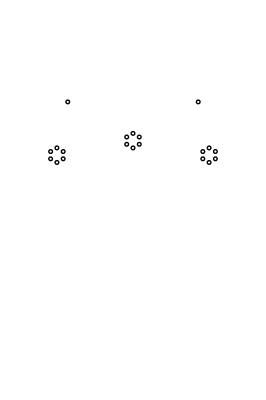

```mathematica
xc={-10.5,-9.63397459621556,-9.63397459621556,-10.5,-11.36602540378444,-11.36602540378444,0.,0.8660254037844386,0.8660254037844386,0.,-0.8660254037844386,-0.8660254037844386,10.5,11.36602540378444,11.36602540378444,10.5,9.63397459621556,9.63397459621556,-9.,9.};
 yc={27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,29.67,30.17,31.17,31.67,31.17,30.17,27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,36.00333333333333,36.00333333333333};
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-15,15},{0,45}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
ncond=Length[xc];
nfeixe=6;
nfases=3;
npr=2;
```

```mathematica
(* rf=.908 *10^-2; *)
rf=29.591*10^-3/2;
rint=7.3914*10^-3/2; 
rpr=4.57*10^-3;
```

```mathematica
ϵ=8.854 10^-12;
```

```mathematica
ρ00=0.06114292531162*10^-3 * π* rf^2;
ρpr=4.19*10^-3* π  *rpr^2;
```

```mathematica
ρsolo= 100;
tempfase=60;
fencalum=0.750223;
αtemp=0.00454562;
σc=fencalum/(ρ00(1+αtemp tempfase));
ρc=1/σc;
```

Dados de simulação

Freqüências de interesse

```mathematica
d1=0.1;
d2=N[6,40];
n=1500;
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,-2,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,1,np-2}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,n];
f2=freqlin[10^d1, 10^d2,n];
f=Sort@Join[f1,f2];
```

```mathematica
f;
```

```mathematica
sk=2*π*f;
nf=Length[sk]
```

3000

```mathematica
sigma=1/ρsolo;
(*kprima[sigma_,Omega_]:=(sigma)+(10^-6)*(0.057849+I*0.12097)*(Omega^0.71603);*)
kprima[sigma_,Omega_]:=(sigma);
G1=DiagonalMatrix[Table[10^-12,{nfases}]];
```

# Outros Calculos

```mathematica
recompmatr[Matr_]:=Module[{ncond2,k,Mrecomp},
ncond2=Solve[Sqrt[2*Min[Dimensions[Matr]]-x]==x,x][[1,1,2]];
Mrecomp=Table[0,{ncond2},{ncond2}];
For[k=1,k<ncond2+1,k++,Mrecomp[[All,k]]=Flatten[{Take[Matr,{k*(k-1)/2+1,k*(k+1)/2}],Table[0,{ncond2-k}]}]];
Table[Mrecomp[[j,i]]=Mrecomp[[i,j]],{i,1,ncond2},{j,1,ncond2}];
Return[{Mrecomp}]]
```

```mathematica
recompmatrlarga[Matr_]:=Module[{YsAux,Ys,k},
YsAux=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]}];
For[k=1,k≤ N[Max[Dimensions[Matr]]],k++,YsAux[[k]]=recompmatr[Matr[[k]]]];
Ys=Flatten[YsAux,1];
Return[{Ys}]]
```

```mathematica
descompmatrlarga[Matr_]:=Module[{kk,nm,Matr2},
Matr2=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]*(N[Min[Dimensions[Matr]]]+1)/2}];
For[nm=1,nm≤N[Max[Dimensions[Matr]]],nm++,
kk=0;
Table[If[ i≥ j,kk++;Matr2[[nm,kk]]=Matr[[nm,i,j]]],{i,1,N[Min[Dimensions[Matr]]]},{j,1,N[Min[Dimensions[Matr]]]}]];
Return[{Matr2}]]
```

## Calculo parametros con P

### Procesamiento de Ynodal

```mathematica
YNodal=Table[0,{nf}];
YNodalA=YNodalB=YNodalC=YNodalD=YNodalE=YNodalF=ytraco=YNodal;
```

```mathematica
compr2=50000.0;
n=20;
Nelem=2^n;
compr=compr2/Nelem;
```

```mathematica
AbsoluteTiming[Do[{ω=sk[[nm]],
MontaMatrizes[ncond,npr,nfeixe,kprima[sigma,ω],ρc,ρpr,rf,rint,rpr,xc,yc,ω],
(*MontaMatrizessemp[ncond,npr,nfeixe,sigma,ρc,ρpr,rf,rint,rpr,xc,yc,ω]*)
Yn=Ynodal[Z1,Y1,compr];
YnM=ArrayFlatten[{{Inverse[Z1 compr]+Y1 compr ,-Inverse[Z1 compr]},{-Inverse[Z1 compr], Inverse[Z1 compr] +Y1 compr}}],
Quad2=MatrixPower[Y2Quad[YnM],(compr2/compr)],
QuadFinal=MatrixPower[Y2Quad[Yn],(compr2/compr)],
YNodal[[nm]]=Ynodal[Z1,Y1,(compr2/compr)*compr],(*Matriz Yn para compr2*)
YNodalB[[nm]]=Quad2Ym[Quad2],  (*Matriz YnSCZ-1 Y2Quad->QuadY2 a la potencia*)
(*YNodalA[[nm]]=Quad2Ym[QuadFinal],  (*Matriz Yn Y2Quad->QuadY2 a la potencia*)
YNodalC[[nm]]=ArrayFlatten[{{Inverse[Z1 compr2]+Y1 compr2 ,-Inverse[Z1 compr2]},{-Inverse[Z1 compr2], Inverse[Z1 compr2] +Y1 compr2}}],
 (*Matriz YnSCZ-1 para compr2*)
YNodalD[[nm]]=ArrayFlatten[{{Inverse[Z1 compr]+Y1 compr ,-Inverse[Z1 compr]},{-Inverse[Z1 compr], Inverse[Z1 compr] +Y1 compr}}],
 (*Matriz YnSCZ-1 para compr*)*)
ytraco[[nm]]=Tr[Yn],
E2prima=Inverse[IdentityMatrix[Length[Z1]]-((compr^2)/4)*(Z1.Y1)],
F2prima=Inverse[IdentityMatrix[Length[Z1]]-((compr^2)/4)*(Y1.Z1)],
A2prima=IdentityMatrix[Length[Z1]]+((compr^2)/4)*(E2prima.Z1.Y1),
B2prima=-compr*E2prima.Z1,
C2prima=-compr*E2prima.Y1,
D2prima=IdentityMatrix[Length[Z1]]+((compr^2)/4)*(F2prima.Y1.Z1),
W2prima=ArrayFlatten[{{A2prima,B2prima},{C2prima,D2prima}}],
Wprima=Nest[MatrixPower[#,2]&,W2prima,n],
YNodalF[[nm]]=-Quad2Ym[Wprima]    (*ATENCAO: SIGNO TROCADO PARA QUE OS ELEMENTOS DE YNodalF SEJAM EXATAMENTE IGUAIS AOS DA MATRIZ YNodal*)
},{nm,1,nf}]]
```

{172.65625,Null}

## Parametros con P

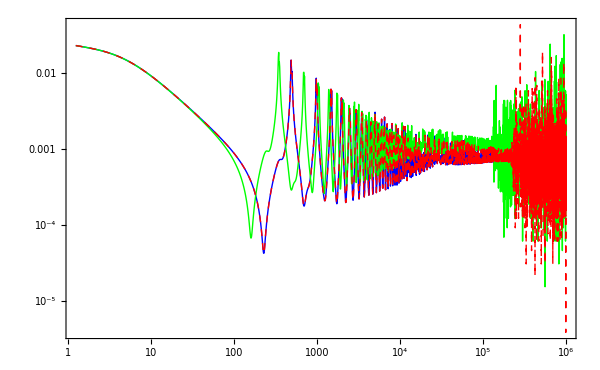

```mathematica
ListLogLogPlot[{
Transpose@{sk/(2 π),Abs[YNodal[[All,1,1]] ]},
Transpose@{sk/(2 π),Abs[YNodalB[[All,1,1]] ]},
Transpose@{sk/(2 π),Abs[YNodalF[[All,1,1]] ]}},Joined->True,PlotRange->All,PlotStyle->{{Blue,Thick},{Green,Thin},{Red,Thick,Dashed}}]
```

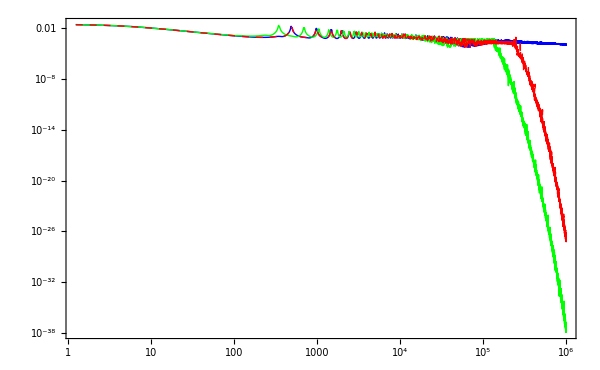

```mathematica
ListLogLogPlot[{
Transpose@{sk/(2 π),Abs[YNodal[[All,4,1]] ]},
Transpose@{sk/(2 π),Abs[YNodalB[[All,4,1]] ]},
Transpose@{sk/(2 π),Abs[YNodalF[[All,4,1]] ]}},Joined->True,PlotRange->All,PlotStyle->{{Blue,Thick},{Green,Thin},{Red,Thick,Dashed}}]
```

```mathematica
{yElem}=descompmatrlarga[YNodal];
{yElemF}=descompmatrlarga[YNodalF];
```

21

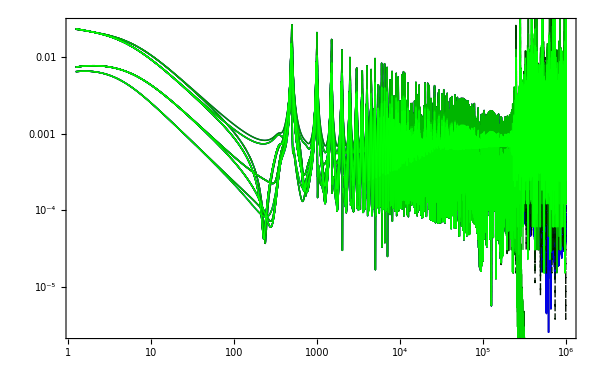

```mathematica
nres=21
Gr1=ListLogLogPlot[Map[Transpose@{sk/(2 π),Abs[yElem[[All,#]]]}&,Range[nres]],Joined->True,PlotRange->All,PlotStyle->Table[{Thin,RGBColor[0,0,i/nres]},{i,nres}]];
Gr2=ListLogLogPlot[Map[Transpose@{sk/(2 π),Abs[yElemF[[All,#]]]}&,Range[nres]],Joined->True,PlotRange->All,PlotStyle->Table[{Thin,Dashed,RGBColor[0,i/nres,0]},{i,nres}]];
Show[Gr1,Gr2]
```

```mathematica
Dimensions[yElem]
```

{3000,21}

```mathematica
(*Export["omega.txt",sk];
Export["yElementos.txt",yElementos];
Export["ytraco.txt",ytraco];*)
```